# Raman Transitions

```mathematica
(*<<AtomicDensityMatrix`*)
```

## Physical Constants

```mathematica
c := 299792458 (*Lichtgeschwindigkeit*)
e := 1.602176565*10^-19 (*Elementarladung*)
Subscript[m, e]:=9.10938291*10^-31(*Elektronenmasse*)
me=9.1093897*10^-31;
Subscript[μ, e]:=-9.28476430*10^-24(*Magnetisches Moment des Elektrons*)
Subscript[g, e]:=-2.00231920436153 (*Lande-Faktor des freien Elektrons*)
hPlanck := 6.62606957*10^-34      (*Plancksches Wirkungsquantum*)
h=6.62606896*10^-34;
hbar:= h/2π
Subscript[k, B]:= 1.3806488*10^-23 (*Boltzmann Konstante*)
kB=1.3806504*10^-23;
μ  := 4Pi*10^-7 (*magnetische Feldkonstante*)
μ0=4*π*10^-7;
ϵ0=1/(c^2*μ0);
ϵ := 8.85418781762*10^-12 (*elektrische Feldkonstante*)
Subscript[a, 0]:=5.2917721092*10^-11 (*Bohrscher Radius*)
Subscript[μ, B]:=9.27400968*10^-24 (*Bohrsches Magneton*)
μN=5.05078343 10^-27; (*Kernmagneton*)
uMass=1.66053873*10^-27;
MassK40 := 39.96399848 *uMass
g=9.81;
Jg=1/2;
S= 1/2;
```

#### Units

```mathematica
km=10^3;
m=1;
cm=10^-2;
mm=10^-3;
μm=10^-6;
nm=10^-9;

THz=10^12;
GHz=10^9;
MHz=10^6;
kHz=10^3;
Hz=1;
mHz=10^-3;
μHz=10^-6;

mK=10^-3;
μK=10^-6;
nK=10^-9;

G=10^-4;
mG=10^-7;

mW=10^-3;
```

#### Nuclear Spin, nuclear magnetic moment, g-factors

```mathematica
Clear[II]
II[K40] = 4; 
II[Rb87] = 3/2; 
II[Na23]=3/2;
II[Li6] = 1; 
μI[K40] = 1.2981*μN; 
μI[Rb87] = 2.75124*μN; 
μI[Na23]=−0.000 80461080μB;
μI[Li6] = -0.82205*μN; 
gs = 2.0023193043737; 
ge[K40] = 2.00229421; 
ge[Na23]=2.00229600;
ge[Rb87] = 2.00233113; 
ge[Li6] = 2.0023193043737;
```

#### Masses

```mathematica
(*Li7=7;Li6=6;Cs=133;Rb87=87;Rb85=85;K40=40; Ca40=41; Yb171=171;Sr88=88;*)
Mass[Li6]=6.015122 uMass;
Mass[Li7]=7.016004 uMass;
Mass[Rb87]=86.9091835 uMass;
Mass[K40]=39.96399867 uMass;
Mass[Cs]=133 uMass; 
Mass[Ca40]=40*uMass; 
Mass[Yb171]=171*uMass;Mass[Sr88]=88*uMass;
```

#### Transition frequencies

```mathematica
λ[Rb87,1]=794.9788509×10^-9;
λ[Rb87,2]=780.246291629×10^-9;
λ[Rb87,3]=420.298×10^-9;
λ[Rb87,4]=421.672×10^-9;

λ[K40,1]=770.1093×10^-9;
λ[K40,2]=766.7021×10^-9;
λ[K40,3]=404.8356×10^-9;
λ[K40,4]=404.5285×10^-9;

λ[Li6,1]=670.992421 10^-9(*Gehm*);
λ[Li6,2]=670.977338 10^-9(*Gehm*);
λ[Li6,3]=323.3590 10^-9;
λ[Li6,4]=323.3590 10^-9;

λ[Sr88,1]:=407.771×10^-9;
λ[Sr88,2]:=421.552×10^-9;

λ[Ca40,1]:=393×10^-9;
λ[Ca40,2]:=397×10^-9;

λ[Yb171,1]:=369×10^-9;
λ[Yb171,2]:=329×10^-9;

λ0[isotope_]:=(λ[isotope,1]+λ[isotope,2])/2;
```

#### Line widths

```mathematica
(*Aus NIST-Tabelle:Linienbreiten (Spalte Aki aus Spectral Database) *)
Γ[Rb87,1]=2 Pi*5.746  10^6;(* Rb D1/D2 Daten aus Paper von Daniel A. Steck *)
Γ[Rb87,2]=2 Pi* 6.065 10^6;(* Rb D1/D2 Daten aus Paper von Daniel A. Steck *)
Γ[Rb87,3]=1.50*10^6;
Γ[Rb87,4]=1.77*10^6;

Γ[K40,1]=3.82*10^7;
Γ[K40,2]=3.87*10^7;
Γ[K40,3]=1.24*10^6;
Γ[K40,4]=1.24*10^6;

Γ[Li6,1]=2π 5.8724 10^6  (*Gehm*);
Γ[Li6,2]=2π 5.8724 10^6  (*Gehm*);
Γ[Li6,3]=1.17 10^6;
Γ[Li6,4]=1.17 10^6;

Γ[Ca40,1]=2 Pi*20  10^6;
Γ[Ca40,2]=2 Pi*20  10^6;

Γ[Sr88,1]=1.28 10^8;
Γ[Sr88,2]=1.42 10^8;

Γ[Yb171,1]=1.4  10^8;
Γ[Yb171,2]=1.8 10^8;

Γ0[isotope_]:=(Γ[isotope,1]+Γ[isotope,2])/2;
```

#### Saturation Intensity

```mathematica
Isat[K40,2]=17.5; (* Subscript[D, 2]-Linie: 17.5 W/m^2 -> Tiecke *)
```

#### g-factors

```mathematica
Clear[gJ, gF, gI]
```

```mathematica
gL[isotope_]:=1-me/Mass[isotope];
gI[isotope_]:=μI[isotope]/(μB* II[isotope]);
gJexact[L_,J_,isotope_]:=gL[isotope]*(J(J+1)-S(S+1)+L(L+1))/(2*J(J+1))+gs*(J(J+1)+S(S+1)-L(L+1))/(2*J(J+1));
gJ[L_,J_,isotope_]:=1+(J(J+1)+S(S+1)-L(L+1))/(2*J(J+1));
gFexact[L_,J_,F_,isotope_]:=gJ[L,J,isotope]*(F(F+1)-II[isotope](II[isotope]+1)+J(J+1))/(2*F(F+1))+gI[isotope]*(F(F+1)-II[isotope](II[isotope]+1)+J(J+1))/(2*F(F+1));
gF[L_,J_,F_,isotope_]:=gJ[L,J,isotope]*(F(F+1)-II[isotope](II[isotope]+1)+J(J+1))/(2*F(F+1))
```

#### Hyperfine constants

```mathematica
HFA[K40,Ground] = -285.7308;
HFA[K40,D1] := -34.49
HFA[K40,D2] := -7.585
HFB[K40,D2]:= -3.445
HFA[Li6,Ground] = 152.1368407;
HFA[Li6,D1] := 17.386;
HFA[Li6,D2] := -1.155;
HFB[Li6,D2]:= -0.10;
HFA[Na23,Ground]:=885.81306440;
HFA[Na23,D1]:=94.44;
HFA[Na23,D2]:=18.534;
HFB[Na23,D2]:=2.724;
```

```mathematica
HFB[K40,D1]:= 0
HFB[Li6,D1]:= 0
HFB[K40,Ground]:= 0
HFB[Li6,Ground]:= 0
HFB[Na23,Ground]:=0;
HFB[Na23,D1]:=0;
```

#### Properties of the D1-line

```mathematica
Subscript[λ, D2]:=670.977338*10^-9
Subscript[ν, D2]:=446.799677*10^12
Subscript[ν, D1]:=446.789634*10^12
Subscript[τ, tot]:=26.79*10^-9
τ[1/2]=27.102*10^-9;
τ[3/2]=27.102 *10^-9;
ΓNat := 5.8724*10^6
μD1:=-2.812*10^-29;
μD2:=3.977*10^-29;
ISat:=(π*h*c)/(3*Subscript[λ, D2]^3*Subscript[τ, tot])
ISatt[A_,ma_,B_,mb_]:=1/4 ϵ*c(hbar/(( Abs[Coeff[A,ma,B,mb]])*μD2*Subscript[τ, tot]))^2;
ReducedMatrixEl = √((2 3 hbar c^3 π ϵ ΓNat*2π)/(2π Subscript[ν, D1])^3);(*Formula acccording to mcKay (phd thesis) yields different value than LeBlancs paper*);
```

```mathematica
ΓΓ[3/2] = (2π Subscript[ν, D2])^3/(3 hbar c^3 π ϵ)μD2^2/(2*3/2+1)1/(2π);
ΓΓ[1/2] = (2π Subscript[ν, D1])^3/(3 hbar c^3 π ϵ)μD1^2/(2*1/2+1)1/(2π);
```

## Diagonalizing magnetic field dependent Hamiltonian

```mathematica
elem=Li6;
```

### State vector definition

```mathematica
J=1/2;
StateVector[Ground]=  Flatten[Table[{mj,mi},{mj,-J,J,1},{mi,II[elem],-II[elem],-1}],1];
StateVector[D1] =  StateVector[Ground] ;
J=3/2;
StateVector[D2]=Flatten[Table[{mj,mi},{mj,-J,J,1},{mi,II[elem],-II[elem],-1}],1];
Clear[J];
```

```mathematica
μB = 8.794100744801886;
```

### Constructing the Hamiltonian

```mathematica
mJ[State_,i_]:=StateVector[State]⟦i,1⟧
mI[State_,i_] :=StateVector[State]⟦i,2⟧
```

```mathematica
UnitOperator[A_,B_]:= If[A==B,1,0] 
IJOp[A_,B_,State_, j_] := If[A==B,mJ[State,j]*mI[State,j],0] 
IJOp1[i_,j_,State_,J_,I_]:=KroneckerDelta[mJ[State,j],mJ[State,i]+1] *KroneckerDelta[ mI[State,j],mI[State,i]-1]*1/2 √((J+mJ[State,j])((J+1)-mJ[State,j])(I-mI[State,j])((I+1)+mI[State,j]))
IJOp2[i_,j_,State_,J_,I_]:=KroneckerDelta[mJ[State,j],mJ[State,i]-1]KroneckerDelta[ mI[State,j],mI[State,i]+1]*1/2 √((J-mJ[State,j])((J+1)+mJ[State,j])(I+mI[State,j])((I+1)-mI[State,j]))
JZOP [A_,B_,State_,j_]:=If[A==B,mJ[State,j],0]
IzOP [A_,B_,State_,j_]:=If[A==B,mI[State,j],0]

fOp[i_,j_,State_]  := KroneckerDelta[mJ[State,j],mJ[State,i]] *KroneckerDelta[ mI[State,j],mI[State,i]]*1/2(3/2 mI[State,j]^2-II[elem](II[elem]+1))(3 mJ[State,j]^2-3/2(3/2+1))+KroneckerDelta[mJ[State,j],mJ[State,i]+1] *KroneckerDelta[ mI[State,j],mI[State,i]-1]*3/4(2mJ[State,j]+1)(2mI[State,j]-1)*((3/2-mJ[State,j])(3/2+mJ[State,j]+1)(II[elem]+mI[State,j])(II[elem]-mI[State,j]+1))^(1/2)+KroneckerDelta[mJ[State,j],mJ[State,i]-1]KroneckerDelta[ mI[State,j],mI[State,i]+1]*3/4(2mJ[State,j]-1)(2mI[State,j]+1)*((3/2+mJ[State,j])(3/2-mJ[State,j]+1)(II[elem]-mI[State,j])(II[elem]+mI[State,j]+1))^(1/2)+KroneckerDelta[mJ[State,j],mJ[State,i]-2]KroneckerDelta[ mI[State,j],mI[State,i]+2]*3/4((3/2+mJ[State,j])((3/2+mJ[State,j]+1))(3/2-mJ[State,j]+1)(3/2-mJ[State,j]+2)*(II[elem]-mI[State,j])(II[elem]-mI[State,j]-1)(II[elem]+mI[State,j]+1)(II[elem]+mI[State,j]+2))^(1/2)+KroneckerDelta[mJ[State,j],mJ[State,i]+2]KroneckerDelta[ mI[State,j],mI[State,i]-2]*3/4((3/2-mJ[State,j])((3/2-mJ[State,j]-1))(3/2+mJ[State,j]+1)(3/2+mJ[State,j]+2)*(II[elem]+mI[State,j])(II[elem]+mI[State,j]-1)(II[elem]-mI[State,j]+1)(II[elem]-mI[State,j]+2))^(1/2)
```

```mathematica
HOperator[A_,B_,i_,j_,isotope_, State_,L_,J_,I_]:=HFA[isotope,State]*(IJOp[A,B,State,j]+IJOp1[i,j,State,J,I]+IJOp2[i,j,State,J,I])+HFB[isotope,State]*If[J>1/2,fOp[i,j,State]/(2*I(2*I-1)J(2J-1)),0]+μB/(2π)*(gJ[L,J,isotope] *JZOP [A,B,State,j]+gI[isotope]* IzOP [A,B,State,j])*MagneticField
```

### SET THE B-FIELD HERE!!

```mathematica
BField :=50;
```

### S_(1/2) - Ground State

```mathematica
(hs =Table[HOperator[StateVector[Ground]⟦i⟧,StateVector[Ground]⟦j⟧, i,j,elem,Ground,0,1/2,II[elem]]/.MagneticField-> BField,{i,Length[StateVector[Ground]]},{j,Length[StateVector[Ground]]}])//MatrixForm;
MatrixForm/@({Energies,States}=Eigensystem[hs]);
MatrixForm/@({energies = Energies[[Ordering[Energies]]],states =States[[Ordering[Energies]]]});
MatrixForm[states,TableHeadings->{energies,StateVector[Ground]}]
```

( | {-1/2,1} | {-1/2,0} | {-1/2,-1} | {1/2,1} | {1/2,0} | {1/2,-1}
-190.481 | -0.924268 | -1.11022×10^-16 | 0. | 1.11022×10^-16 | 0.381744 | 0.
-150.255 | 0. | -0.801461 | 0. | 0. | 0. | 0.598046
6.08719 | 0. | 0. | -1. | -2.00968×10^-16 | 0. | 0.
74.1862 | 0. | -0.598046 | 0. | 0. | 0. | -0.801461
114.413 | 0.381744 | -2.22045×10^-16 | 0. | 0. | 0.924268 | 0.
146.05 | -1.32099×10^-16 | 0. | 8.99452×10^-17 | -1. | 0. | 0.)

```mathematica
Clear[b]
```

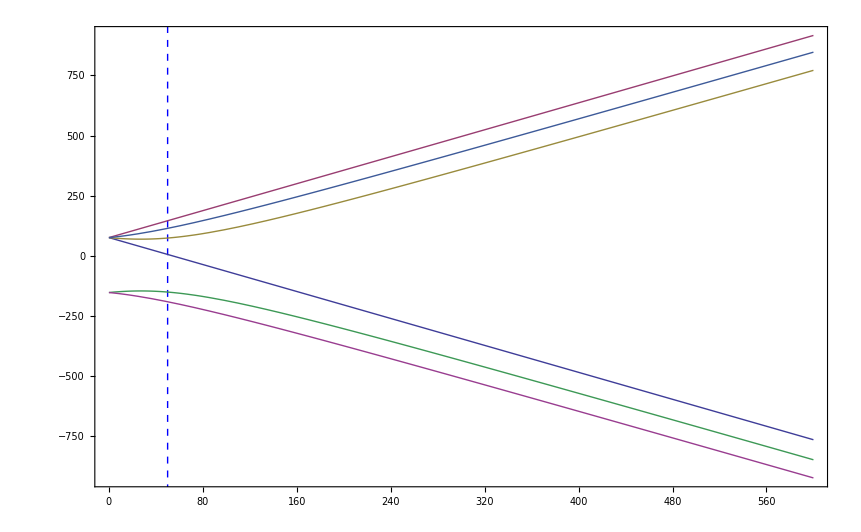

```mathematica
(BreitRabiGround=Table[HOperator[StateVector[Ground]⟦i⟧,StateVector[Ground]⟦j⟧, i,j,elem,Ground,0,1/2,II[elem]]/.MagneticField-> b,{i,Length[StateVector[Ground]]},{j,Length[StateVector[Ground]]}])//MatrixForm;
Quiet[MatrixForm/@({EE,SS}=Eigensystem[BreitRabiGround])];
Plot[EE,{b,0,600}, Frame -> True, Prolog -> {Dashed,Blue,Line[{{BField,-2000},{BField,2000}}]}]
```

### P_(1/2)- D1-States

```mathematica
Clear[ht,hs,D1,D2]
```

```mathematica
(ht =Table[HOperator[StateVector[D1]⟦i⟧,StateVector[D1]⟦j⟧, i,j,elem,D1,1,1/2,II[elem]]/.MagneticField-> BField,{i,Length[StateVector[D1]]},{j,Length[StateVector[D1]]}])//MatrixForm;
MatrixForm/@({EnergiesD1,StatesD1}=Eigensystem[ht]);
MatrixForm/@{energiesD1=EnergiesD1[[Ordering[EnergiesD1]]],statesD1=StatesD1[[Ordering[EnergiesD1]]]};
MatrixForm[statesD1,TableHeadings->{energiesD1,StateVector[D1]}]
```

( | {-1/2,1} | {-1/2,0} | {-1/2,-1} | {1/2,1} | {1/2,0} | {1/2,-1}
-34.6279 | 0.978233 | 0. | 0. | 0. | -0.207509 | 0.
-26.9606 | 0. | -0.95899 | 0. | 0. | 0. | 0.28344
-14.6341 | 0. | 0. | 1. | 0. | 0. | 0.
18.2676 | 0. | 0.28344 | 0. | 0. | 0. | 0.95899
25.9349 | -0.207509 | 0. | 0. | 0. | -0.978233 | 0.
32.0201 | 0. | 0. | 0. | 1. | 0. | 0.)

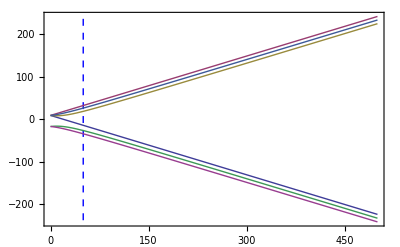

```mathematica
(BreitRabiD1=Table[HOperator[StateVector[D1]⟦i⟧,StateVector[D1]⟦j⟧, i,j,elem,D1,1,1/2,II[elem]]/.MagneticField-> b,{i,Length[StateVector[D1]]},{j,Length[StateVector[D1]]}]);
Quiet[MatrixForm/@({ED1,SD1}=Eigensystem[BreitRabiD1])];
Plot[ED1,{b,0,500}, Frame -> True, Prolog -> {Dashed,Blue,Line[{{BField,-2000},{BField,2000}}]}]
```

### D2-States

```mathematica
(hD2=Table[HOperator[StateVector[D2]⟦i⟧,StateVector[D2]⟦j⟧, i,j,elem,D2,1,3/2,II[elem]]/.MagneticField-> BField,{i,Length[StateVector[D2]]},{j,Length[StateVector[D2]]}])//MatrixForm;
MatrixForm/@({EnergiesD2,StatesD2}=Eigensystem[hD2]);
MatrixForm/@({energiesD2 =EnergiesD2[[Ordering[EnergiesD2]]],statesD2 =StatesD2[[Ordering[EnergiesD2]]]});
MatrixForm[statesD2, TableHeadings->{energiesD2,StateVector[D2]}]
```

( | {-3/2,1} | {-3/2,0} | {-3/2,-1} | {-1/2,1} | {-1/2,0} | {-1/2,-1} | {1/2,1} | {1/2,0} | {1/2,-1} | {3/2,1} | {3/2,0} | {3/2,-1}
-141.682 | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-139.934 | 0. | -0.999884 | 0. | 0. | 0. | -0.0152597 | 0. | 0. | 0. | 0. | 0. | 0.
-138.239 | 0.999881 | 0. | 0. | 0. | 0.0154544 | 0. | 0. | 0. | 0.000131011 | 0. | 0. | 0.
-47.2226 | 0. | -0.0152597 | 0. | 0. | 0. | 0.999884 | 0. | 0. | 0. | 0. | 0. | 0.
-46.7096 | -0.0154546 | 0. | 0. | 0. | 0.999741 | 0. | 0. | 0. | 0.0167337 | 0. | 0. | 0.
-46.1169 | 0. | 0. | 0. | 0.999845 | 0. | 0. | 0. | 0.0176158 | 0. | 0. | 0. | 0.000132671
46.0429 | -5.40633×10^-22 | 0. | 0. | 0. | 7.04217×10^-20 | 0. | -0.999887 | 0. | -3.24807×10^-18 | 0. | -0.0150519 | 0.
46.6108 | 0. | 0. | 0. | -0.0169556 | 0. | 0. | 0. | 0.999746 | 0. | 0. | 0. | 0.0148714
47.2465 | 0.000132602 | 0. | 0. | 0. | -0.0173853 | 0. | 0. | 0. | 0.999849 | 0. | 0. | 0.
138.242 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
140.034 | -1.20909×10^-20 | 0. | 0. | 0. | 2.37832×10^-18 | 0. | 0.0150519 | 0. | -2.2206×10^-16 | 0. | -0.999887 | 0.
141.728 | 0. | 0. | 0. | 0.000124485 | 0. | 0. | 0. | -0.0148713 | 0. | 0. | 0. | 0.999889)

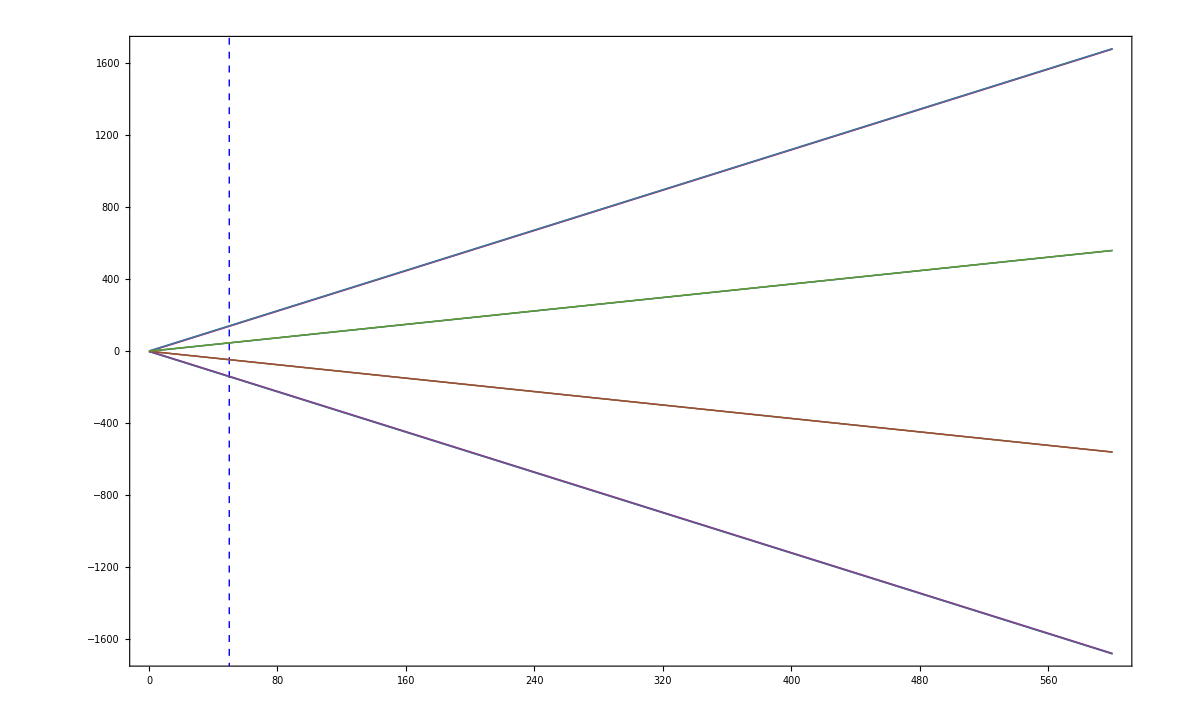

```mathematica
(BreitRabiD2=Table[HOperator[StateVector[D2]⟦i⟧,StateVector[D2]⟦j⟧, i,j,elem,D2,1,3/2,II[elem]]/.MagneticField-> b,{i,Length[StateVector[D2]]},{j,Length[StateVector[D2]]}])//MatrixForm;
Quiet[MatrixForm/@({ED2,SD2}=Eigensystem[BreitRabiD2])];
Plot[ED2,{b,0,600}, Frame -> True, Prolog -> {Dashed,Blue,Line[{{BField,-2000},{BField,2000}}]}]
```

### D1-Transitions

```mathematica
Clear[q]
D1TransitionElement[i_,j_,qPolarization_]:=Quiet[Round[Sum[Sum[Select[statesD1⟦j⟧,#≠0&]⟦s⟧*Select[states⟦i⟧,#≠0&]⟦r⟧*(-1)^(-1/2+StateVector[D1]⟦Position[statesD1⟦j⟧,Select[statesD1⟦j⟧,#≠0&]⟦s⟧]⟦1,1⟧⟧⟦1⟧)ThreeJSymbol[{1/2,StateVector[Ground]⟦Position[states⟦i⟧,Select[states⟦i⟧,#≠0&]⟦r⟧]⟦1,1⟧⟧⟦1⟧},{1,qPolarization},{1/2,-StateVector[D1]⟦Position[statesD1⟦j⟧,Select[statesD1⟦j⟧,#≠0&]⟦s⟧]⟦1,1⟧⟧⟦1⟧}]*KroneckerDelta[StateVector[Ground]⟦Position[states⟦i⟧,Select[states⟦i⟧,#≠0&]⟦r⟧]⟦1,1⟧⟧⟦2⟧,StateVector[Ground]⟦Position[statesD1⟦j⟧,Select[statesD1⟦j⟧,#≠0&]⟦s⟧]⟦1,1⟧⟧⟦2⟧],{r,1,Length[Select[states⟦i⟧,#≠0&]]}],{s,1,Length[Select[statesD1⟦j⟧,#≠0&]]}],0.001]];
MatrixForm[Table[D1TransitionElement[i,j,0],{i,Length[StateVector[Ground]]},{j,Length[StateVector[D1]]}],TableHeadings -> {Table[i,{i,Length[StateVector[Ground]]}],Table[i "D1",{i,Length[StateVector[D1]]}]}]
```

( | D1 | 2 D1 | 3 D1 | 4 D1 | 5 D1 | 6 D1
1 | 0.337 | 0. | 0. | 0. | -0.231 | 0.
2 | 0. | -0.245 | 0. | 0.327 | 0. | 0.
3 | 0. | 0. | 0.408 | 0. | 0. | 0.
4 | 0. | -0.327 | 0. | -0.245 | 0. | 0.
5 | -0.231 | 0. | 0. | 0. | -0.337 | 0.
6 | 0. | 0. | 0. | 0. | 0. | -0.408)

### D2 Transitions

```mathematica
Off[ClebschGordan::phy];
D2TransitionElement[i_,j_,qPolarization_]:=Round[Sum[Sum[Select[statesD2⟦j⟧,#≠0&]⟦s⟧*Select[states⟦i⟧,#≠0&]⟦r⟧*(-1)^(3/2-1+StateVector[D2]⟦Position[statesD2⟦j⟧,Select[statesD2⟦j⟧,#≠0&]⟦s⟧]⟦1,1⟧⟧⟦1⟧)ThreeJSymbol[{1/2,StateVector[Ground]⟦Position[states⟦i⟧,Select[states⟦i⟧,#≠0&]⟦r⟧]⟦1,1⟧⟧⟦1⟧},{1,qPolarization},{3/2,-StateVector[D2]⟦Position[statesD2⟦j⟧,Select[statesD2⟦j⟧,#≠0&]⟦s⟧]⟦1,1⟧⟧⟦1⟧}]*KroneckerDelta[StateVector[Ground]⟦Position[states⟦i⟧,Select[states⟦i⟧,#≠0&]⟦r⟧]⟦1,1⟧⟧⟦2⟧,StateVector[D2]⟦Position[statesD2⟦j⟧,Select[statesD2⟦j⟧,#≠0&]⟦s⟧]⟦1,1⟧⟧⟦2⟧],{r,1,Length[Select[states⟦i⟧,#≠0&]]}],{s,1,Length[Select[statesD2⟦j⟧,#≠0&]]}],0.001]
MatrixForm[Table[D2TransitionElement[i,j,1],{i,Length[StateVector[Ground]]},{j,Length[StateVector[D2]]}],TableHeadings -> {Table[i,{i,Length[StateVector[Ground]]}],Table[i "D2",{i,Length[StateVector[D2]]}]}]
```

( | D2 | 2 D2 | 3 D2 | 4 D2 | 5 D2 | 6 D2 | 7 D2 | 8 D2 | 9 D2 | 10 D2 | 11 D2 | 12 D2
1 | 0. | 0. | 0. | 0. | 0. | 0. | -0.264 | 0. | 0. | 0. | 0.195 | 0.
2 | 0. | 0. | 0. | 0. | 0. | 0.004 | 0. | 0.227 | 0. | 0. | 0. | -0.302
3 | 0. | 0. | 0. | 0. | 0.005 | 0. | 0. | 0. | 0.289 | 0. | 0. | 0.
4 | 0. | 0. | 0. | 0. | 0. | 0.003 | 0. | 0.179 | 0. | 0. | 0. | 0.398
5 | 0. | 0. | 0. | 0. | 0. | 0. | 0.117 | 0. | 0. | 0. | 0.46 | 0.
6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.5 | 0. | 0.)

### Spectrum

```mathematica
Lorentzian [ω_,ω0_,strength_]:= strength/(1+4(ω-ω0)^2/((Γ[elem,2]/(2 π 10^6))^2))
```

```mathematica
energies[[4]]-HFA[elem,Ground]/2
```

-1.88222

```mathematica
res=Table[Sort[Flatten[Table[{energies[[i]]-HFA[elem,Ground]/2-energiesD2[[j]],Abs[D2TransitionElement[i,j,q]]^2},{i,6,6},{j,1,Length[StateVector[D2]]}],1]],{q,-1,1}];
```

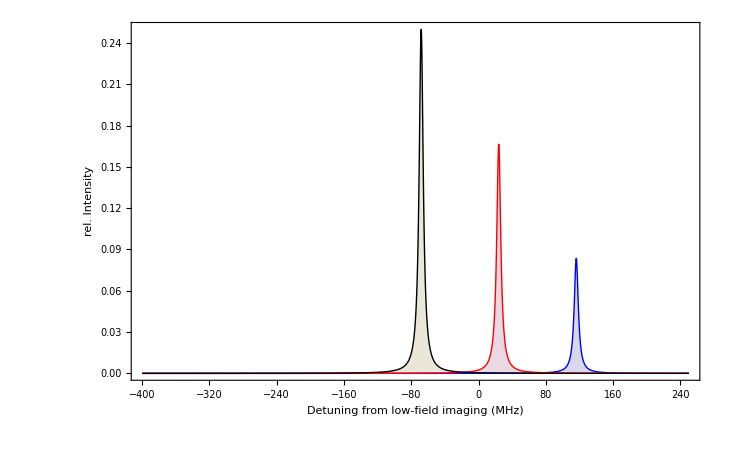

```mathematica
Spektrum = Plot[{Sum[Lorentzian[x,res[[1,ii,1]],res[[1,ii,2]]],{ii,Length[res[[1]]]}],Sum[Lorentzian[x,res[[2,ii,1]],res[[2,ii,2]]],{ii,Length[res[[2]]]}],Sum[Lorentzian[x,res[[3,ii,1]],res[[3,ii,2]]],{ii,Length[res[[3]]]}]},{x,-400,250}, PlotRange -> All,PlotStyle -> {Blue,Red,Black}, Filling -> Bottom,Frame -> True,FrameLabel -> {"Detuning from low-field imaging (MHz)","rel. Intensity"}, LabelStyle->{Gray,Medium}]
```

### Intensity for Raman sweeps

```mathematica
Delta :=2π* 10*10^9
RabiEff:=2π*10^4
Waist := 150 10^-6 (*horizontal Beam*)
ExArea= π Waist^2//N;(*horizontal Beam*)
PRaman1 = 1.10 10^-4;(*horizontal Beam*)
IRaman1 := PRaman1/(π Waist^2) (*horizontal Beam*)
IRaman2[Delta1_,RabiEff_]:=(ϵ*c)^2((Subscript[μ, D1]^4*(.054148)^2)/(hbar^4*Delta1^2*RabiEff^2))^-1 /IRaman1
PRaman2[Delta1_,RabiEff_] := IRaman2[Delta1,RabiEff]*(π*(100 10^-6)^2)*1000
```

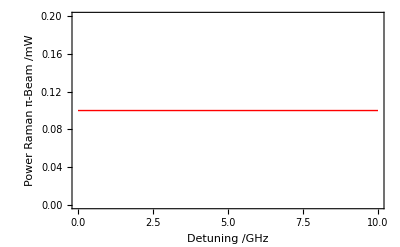

```mathematica
freq := {1*RabiEff/(2π),2*RabiEff/(2π),3*RabiEff/(2π),4*RabiEff/(2π)}
p1 =Plot[PRaman2[2π  x*10^9,2π freq ],{x,.0,Delta/(2π 10^9)},PlotRange->{0,.2},PlotStyle->{Blue,Thick}];
p2 = Plot[.1,{x,.0*Delta/(2π 10^9),Delta/(2π 10^9)}, PlotStyle->{Red,Thick}];
Show[p1,p2, Frame -> True, FrameLabel -> {"Detuning /GHz", "Power Raman π-Beam /mW"}, LabelStyle ->{Medium,Bold}]
```

```mathematica
CGCG := 0.0414
PVert := 1.6 10^-6;
LineX :=√5 10^-6;
LineY:= √77 10^-6;
IVert :=  PVert/(LineX LineY);
```

```mathematica
EffectiveRabiFreq =μD1^2*√IRaman1*√IVert*CGCG /(hbar^2 Delta ϵ c)
```

2041.06

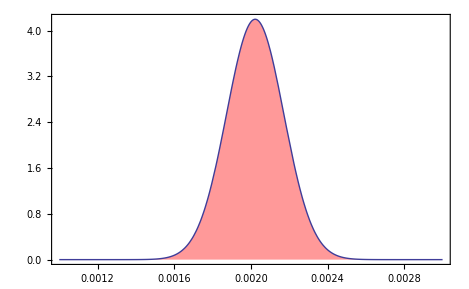

```mathematica
Ω[t_]:= Exp[(-(t-0.002)^2)/(((.5 10^-3)/(2 √Log[2]//N))^2)] EffectiveRabiFreq
c2[δ_,t_] := Ω[t]/2(1-Exp[-ⅈ(Delta-δ)t])/(Delta +δ)-Ω[t]/2(1-Exp[-ⅈ δ t])/δ
Plot[Abs[c2[100,x]]^2,{x,0.001,0.003},PlotRange->All,Mesh-> None,Filling->Axis,FillingStyle-> Directive[Opacity[.4],Red],Frame->True]
```

## AC-Stark Shift

### 1st Method

```mathematica
FF = 9/2;
JJ = 1/2;
gJGround = 2.00229421;
gF = (FF(FF+1)+JJ(JJ+1)-II(II+1))/(2FF(FF+1))gJGround
```

0.0404504 (51/2-II (1+II))

```mathematica
LightShift[Δ_,q_,mF_,Iq_]:= -(c^2 π)/(hPlanck 2)Iq(ΓNat/(Subscript[ν, D2])^3(2-q gF  mF)(1/Δ+1/(Subscript[ν, D2]+(Subscript[ν, D2]-Δ)))+ΓNat/(Subscript[ν, D1])^3(1+q gF  mF)(1/(Subscript[ν, D1]-(Subscript[ν, D2]-Δ))+1/(Subscript[ν, D1]+(Subscript[ν, D2]-Δ))))
Plot[{LightShift[Δ,1,-9/2,1 10^6]-LightShift[Δ,1,-7/2,1 10^6],LightShift[Δ,-1,-9/2,1 10^6]-LightShift[Δ,-1,-7/2,1 10^6]},{Δ,-100*  10^9,-5 10^9},Frame -> True,FrameLabel->{"Detuning from D2 [Hz]", "Differential Light Shift [Hz]"},Axes -> False,PlotStyle->Thick]
```

-Graphics-

### 2nd Method

```mathematica
ScalarLightShift[ω_]:=-(c^2 π)/(hPlanck 2)(ΓΓ[3/2]/(Subscript[ν, D2])^3 2(1/(Subscript[ν, D2]-ω)+1/(Subscript[ν, D2]+ω))+ΓΓ[1/2]/( Subscript[ν, D1])^3(1/(Subscript[ν, D1]-ω)+1/(Subscript[ν, D1]+ω)))
VectorLightShift[ω_]:= -(c^2 π)/(hPlanck 2)(-ΓΓ[3/2]/(Subscript[ν, D2])^3(1/(Subscript[ν, D2]-ω)+1/(Subscript[ν, D2]+ω))+ΓΓ[1/2]/( Subscript[ν, D1])^3(1/(Subscript[ν, D1]-ω)+1/(Subscript[ν, D1]+ω)))
TotalLightShift[ITotal_,IPlus_,IMinus_,ω_,mF_]:= ScalarLightShift[ω]ITotal+VectorLightShift[ω](IPlus - IMinus)(gF mF)
```

```mathematica
Plot[{TotalLightShift[IRaman1 + IVert,IRaman1/2 + IVert,IRaman1/2 ,ω,-7/2]-TotalLightShift[IRaman1 + IVert,IRaman1/2 + IVert,IRaman1/2,ω,-5/2],TotalLightShift[IRaman1 + IVert,IRaman1/2 ,IRaman1/2+ IVert ,ω,-7/2]-TotalLightShift[IRaman1 + IVert,IRaman1/2 ,IRaman1/2+ IVert,ω,-5/2]},{ω,(389.276-.01) 10^12,(389.276+.01) 10^12},Frame -> True,FrameLabel->{"Frequency [Hz]", "Differential Light Shift [Hz]"},Axes -> False,PlotStyle->Thick]
```

-Graphics-

## Heating Rate

```mathematica
Clear[RecoilEnergy, ScalarHeating, VectorHeating]
```

```mathematica
RecoilEnergy[Δ_] := (hbar^2((Subscript[ν, D2]+Δ)/c))/(2MassK40)
```

```mathematica
ScalarHeating[Δ_]:= (c^2 π ((Subscript[ν, D2]+Δ))^3)/(hbar 2)((2 ΓΓ[3/2])/(Subscript[ν, D2])^6(1/Δ+1/(Subscript[ν, D2]+(Subscript[ν, D2]-Δ)))^2+ΓΓ[1/2]/ΓΓ[3/2] ΓΓ[1/2]/( Subscript[ν, D1])^6(1/(Subscript[ν, D1]-(Subscript[ν, D2]-Δ))+1/(Subscript[ν, D1]+(Subscript[ν, D2]-Δ)))^2)
VectorHeating[Δ_]:= (c^2 π ((Subscript[ν, D2]+Δ))^3)/(hbar 2)(-ΓΓ[3/2]/(Subscript[ν, D2])^6(1/Δ+1/(Subscript[ν, D2]+(Subscript[ν, D2]-Δ)))^2+ΓΓ[1/2]/ΓΓ[3/2] ΓΓ[1/2]/(Subscript[ν, D1])^6(1/(Subscript[ν, D1]-(Subscript[ν, D2]-Δ))+1/(Subscript[ν, D1]+(Subscript[ν, D2]-Δ)))^2)
HeatingRate[Δ_,I_,q_,mF_]:=2(*RecoilEnergy[Δ]*)ΓΓ[3/2](ScalarHeating[Δ]I+VectorHeating[Δ](gF mF)q I)
```

Heating Rate vs. Detuning at low magnetic fields for 9/2 and 5/2 atoms shown in blue and red, respectively.

```mathematica
LogPlot[{HeatingRate[Δ,PerturbationIntensity[1,5],-1,-9/2],HeatingRate[Δ,PerturbationIntensity[1,5],-1,-3/2]},{Δ,5*  10^12,-7* 10^12},Frame -> True,FrameLabel -> {"Detuning from D2 Line [Hz]","Scattered Photons [1/s]"},PlotStyle->Thick]
```

-Graphics-

Heating Rate vs. Perturbation Power in mW at low magnetic fields for 9/2 and 5/2 atoms shown in blue and red, respectively.

```mathematica
Plot[{HeatingRate[100 10^9,(P 10^-3)/(π*(5 10^-6)^2),-1,-9/2],HeatingRate[100 10^9,(P 10^-3)/(π*(5 10^-6)^2),-1,-5/2]},{P,0,2},Frame -> True,FrameLabel -> {"Perturbation Power [mW]","Scattered Photons [1/s]"},PlotStyle->Thick]
```

-Graphics-

```mathematica
PP = 1;
PerturbationIntensity[PP_,WW_]:=(PP 10^-3)/(π*(WW 10^-6)^2)
```

```mathematica
HeatingRate[100 10^9,(PP 10^-3)/(π*(5 10^-6)^2),-1,-9/2]
```

1.18993×10^6 (0.00373052+0.0000494129 (51/2-II (1+II)))

## High Field AC Stark-Shift

```mathematica
D1TransitionElements =Table[D1TransitionElement[i,j,q],{i,18},{j,18}];
D2TransitionElements =Table[D2TransitionElement[i,j,q],{i,18},{j,36}];
```

Part::partw: Part 13 of {{0., 0., 1., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., -0.999884, 0., 0., 0., -0.0152597, 0., 0., 0., 0., 0., 0.}, « 8 », {-1.20909×10^-20, 0., 0., 0., 2.37832×10^-18, 0., 0.0150519, 0., -2.2206×10^-16, 0., -0.999887, 0.}, {0., 0., 0., 0.000124485, 0., 0., 0., -0.0148713, 0., 0., 0., 0.999889}} does not exist.

Part::partw: Part 14 of {{0., 0., 1., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., -0.999884, 0., 0., 0., -0.0152597, 0., 0., 0., 0., 0., 0.}, « 8 », {-1.20909×10^-20, 0., 0., 0., 2.37832×10^-18, 0., 0.0150519, 0., -2.2206×10^-16, 0., -0.999887, 0.}, {0., 0., 0., 0.000124485, 0., 0., 0., -0.0148713, 0., 0., 0., 0.999889}} does not exist.

Part::partw: Part 15 of {{0., 0., 1., 0., 0., 0., 0., 0., 0., 0., 0., 0.}, {0., -0.999884, 0., 0., 0., -0.0152597, 0., 0., 0., 0., 0., 0.}, « 8 », {-1.20909×10^-20, 0., 0., 0., 2.37832×10^-18, 0., 0.0150519, 0., -2.2206×10^-16, 0., -0.999887, 0.}, {0., 0., 0., 0.000124485, 0., 0., 0., -0.0148713, 0., 0., 0., 0.999889}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Set the B-Field first and then calculate the matrix elements for D1- and D2 transitions using the Hamiltonian above.
The variable m in the following formulas is the number of the substate in the 4s groundstate, m=1 means the state with lowest energy for a given B-Field. (m=1 is equivalent to m_F=9/2, m=2 to m_F=7/2 etc.)

```mathematica
D2SumOverTrEl=Table[Sum[D2TransitionElements[[m,j]]^2,{j,36}],{m,18}];
D1SumOverTrEl=Table[Sum[D1TransitionElements[[m,j]]^2,{j,18}],{m,18}];
```

### Slow Calculation

```mathematica
HFLightShift1[Δ_,Iq_,m_,q_] := -1/(2 hbar c hPlanck  ϵ)(μD2^2/4(1/(2π (Subscript[ν, D2]-(Subscript[ν, D1]+Δ)))-1/(2π (Subscript[ν, D2]+(Subscript[ν, D1]+Δ))))Iq Sum[Abs[D2TransitionElement[m,j,q]]^2,{j,36}]+μD1^2/2(1/(2π (Subscript[ν, D1]-(Subscript[ν, D1]+Δ)))-1/(2π (Subscript[ν, D1]+(Subscript[ν, D1]+Δ))))Iq Sum[Abs[D1TransitionElement[m,j,q]]^2,{j,18}]); (*factor hPlanck due to conversion between Energy and frequency*)
```

```mathematica
(*Plot[{HFLightShift1[Δ,Ii,1,1]-HFLightShift[Δ,Ii,2,1],HFLightShift[Δ,Ii,1,-1]-HFLightShift[Δ,Ii,2,-1]},{Δ,-100*  10^9,-5 0 10^9},PlotStyle->Thick ,Frame -> True ]*)
```

### Fast Calculation

#### Frequency/Wavelength Conversions

```mathematica
WavelengthToFreq[λ_(*λ in nm*)]:= c/ (λ *10^-9)
WavelengthToFreq[780]//N
```

3.84349×10^14

```mathematica
FreqToWavelength[ν_(* ν in THz*)]:= c/(ν *10^12)*10^9
FreqToWavelength[389.27684]
```

770.127

```mathematica
FreqDetuningToD2Line[λ_] :=  c/ (λ *10^-9)-Subscript[ν, D2] 
FreqDetuningToD1Line[λ_] :=  c/ (λ *10^-9)-Subscript[ν, D1] 
FreqDetuningToD2Line[770.127]
FreqDetuningToD1Line[770.127]
```

-5.7523×10^13

-5.7513×10^13

#### High Field light-shift

```mathematica
HFLightshift[Δ_,m_,I_] := -1/(2 hbar hPlanck  ϵ c)( μD2^2/4(1/(Subscript[ν, D2]-(Subscript[ν, D1]  +Δ))+1/(Subscript[ν, D2]+(Subscript[ν, D1]  +Δ)))I D2SumOverTrEl⟦m⟧+μD1^2/2(1/(Subscript[ν, D1]-(Subscript[ν, D1]  +Δ))+1/(Subscript[ν, D1]+(Subscript[ν, D1]+Δ)))I D1SumOverTrEl⟦m⟧)
```

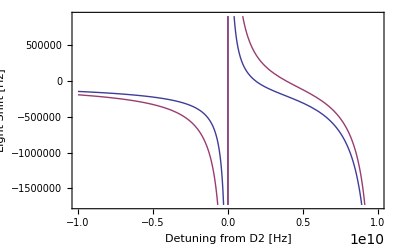

```mathematica
Plot[{(HFLightshift[Δ,1,IVert ]/.q ->-1)+(HFLightshift[Δ,1,IRaman1 ]/.q ->0),(HFLightshift[Δ,2,IVert ]/.q ->-1)+(HFLightshift[Δ,2,IRaman1 ]/.q ->0)} ,{Δ,-10*10^9,10 10^9},PlotStyle->Thick ,Frame -> True,FrameLabel->{"Detuning from D2 [Hz]", "Light Shift [Hz]"}]
```

```mathematica
PerturbationIntensity[.1/50,5]
```

25464.8

```mathematica
Clear[PPower,Waist, mState]
```

```mathematica
PPower = 0.0065 (*mW*);
Waist = 5 (*μm*);
mState = 18;
Detuning = 6.7 10^12 (*Hz*);
Polarisation = 1;
Print["The Lightshift caused by a circular spot of ",Detuning/10^9,"GHz detuned light with Δm=",Polarisation , " Polarisation with radius ", Waist,"μm and a Power of ",PPower,"mW is ",  (HFLightshift[Detuning,mState,PerturbationIntensity[PPower,Waist]]/.q-> Polarisation)/1000, "kHz"]
```

The Lightshift caused by a circular spot of 6700.GHz detuned light with Δm=1 Polarisation with radius 5μm and a Power of 0.0065mW is 0.kHz

Differential Light Shift for different m_F substates

```mathematica
DifferentialLightShift[Δ_,n_,m_,I_]:=Abs[HFLightshift[Δ,n,I]-HFLightshift[Δ,m,I]]/(1/2 Abs[HFLightshift[Δ,n,I]+HFLightshift[Δ,m,I]])
DiffLightShift[Δ_,n_,m_,I_]:=Abs[HFLightshift[Δ,n,I]-HFLightshift[Δ,m,I]]
```

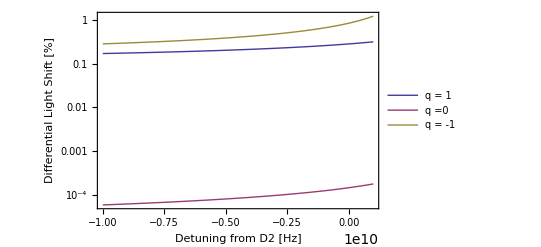

```mathematica
LogPlot[{DifferentialLightShift[Δ,1,2,PerturbationIntensity[.1/50,5]]/.q ->1,DifferentialLightShift[Δ,1,2,PerturbationIntensity[.1/50,5]]/.q ->0,DifferentialLightShift[Δ,1,2,PerturbationIntensity[.1/50,5]]/.q ->-1},{Δ,-10*10^9,1*10^9},PlotStyle->Thick ,Frame -> True,FrameLabel->{"Detuning from D2 [Hz]", "Differential Light Shift [%]"},PlotRange->{0,0.5},PlotLegends->{"q = 1", "q =0","q = -1"}]
```

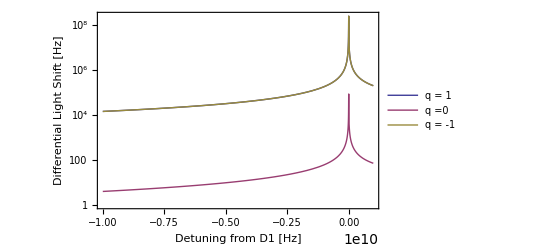

```mathematica
LogPlot[{DiffLightShift[Δ,1,2,PerturbationIntensity[.1/50,5]]/.q ->1,DiffLightShift[Δ,1,2,PerturbationIntensity[.1/50,5]]/.q ->0,DiffLightShift[Δ,1,2,PerturbationIntensity[.1/50,5]]/.q ->-1},{Δ,-10*10^9,1*10^9},PlotRange-> {0,80000},PlotStyle->Thick ,Frame -> True,FrameLabel->{"Detuning from D1 [Hz]", "Differential Light Shift [Hz]"},PlotLegends->{"q = 1", "q =0","q = -1"}]
```

```mathematica
DiffLightShift[-1.7396468739550625*^12,1,3,PerturbationIntensity[.1,5]]/.q->0
```

66.2738

Light Shift for different light polarisations

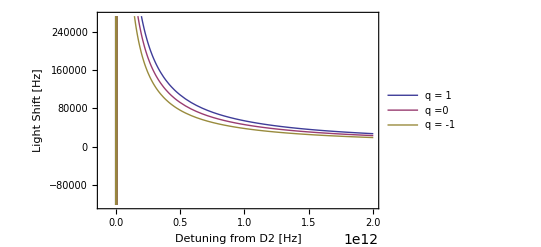

```mathematica
ABS =Plot[{HFLightshift[Δ,1,PerturbationIntensity[.1,5]]/.q-> 1,HFLightshift[Δ,1,PerturbationIntensity[.1,5]]/.q ->0,HFLightshift[Δ,1,PerturbationIntensity[.1,5]]/.q ->-1} ,{Δ,-1*10^11,20*10^11},PlotStyle->Thick ,Frame -> True,FrameLabel->{"Detuning from D2 [Hz]", "Light Shift [Hz]"},PlotLegends->{"q = 1", "q =0","q = -1"}]
```

### High Field heating-rate

```mathematica
HFHeating[Δ_,m_,I_]:=(2((Subscript[ν, D1]+Δ))^3)/(hbar^3 c^3 π 3 ϵ^1) (μD2^4/4 (1/(Subscript[ν, D2]-(Subscript[ν, D1]+Δ))-1/(Subscript[ν, D2]+(Subscript[ν, D1]+Δ)))^2 I D2SumOverTrEl⟦m⟧+μD1^4/2 (1/(Subscript[ν, D1]-(Subscript[ν, D1]+Δ))-1/((*2*) (Subscript[ν, D1]+(Subscript[ν, D1]+Δ))))^2 I D1SumOverTrEl⟦m⟧)
```

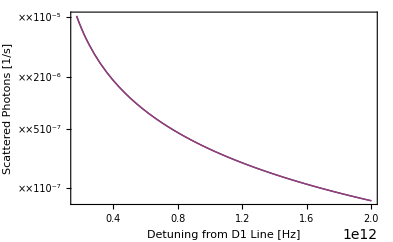

```mathematica
LogPlot[{HFHeating[Δ,1,PerturbationIntensity[.1/50,5]]/.q->-1,HFHeating[Δ,2,PerturbationIntensity[.1/50,5]]/.q->-1},{Δ,173GHz, 2000GHz},PlotStyle->Thick ,Frame -> True,FrameLabel -> {"Detuning from D1 Line [Hz]","Scattered Photons [1/s]"}]
```

```mathematica
HFHeating[6.7 *10^12,1,PerturbationIntensity[.007,5]]/.q->1
```

2.3235×10^-8

```mathematica
HFHeating[6.7 *10^12,3,PerturbationIntensity[.007,5]]/.q->1
```

2.3242×10^-8

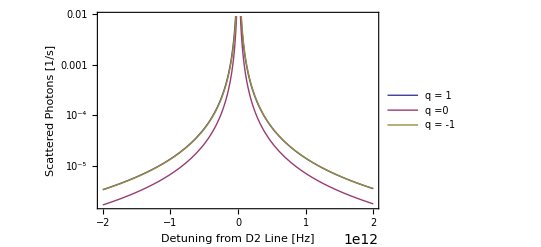

```mathematica
LogPlot[{HFHeating[Δ,1,PerturbationIntensity[.1,5]]/.q->1,HFHeating[Δ,1,PerturbationIntensity[.05,5]]/.q->0,HFHeating[Δ,1,PerturbationIntensity[.1,5]]/.q->-1},{Δ,-2*10^12,2*10^12},PlotStyle->Thick ,Frame -> True,FrameLabel -> {"Detuning from D2 Line [Hz]","Scattered Photons [1/s]"},PlotLegends->{"q = 1", "q =0","q = -1"}]
```

### Side Calculations

```mathematica
PulseLength =Table[10^-3 j,{j,10,100,90}] (*s*);
LogPlot[{(HFHeating[Δ,1,PerturbationIntensity[0.007,5]]/.q->1)*PulseLength,(HFHeating[Δ,3,PerturbationIntensity[0.007,5]]/.q->1)*PulseLength},{Δ,-1*10^12,7*10^12},PlotStyle->{Blue,Red} ,Frame -> True,FrameLabel -> {"Detuning from D2 Line [Hz]","Heating [E_rec]"}];
```

$Aborted

```mathematica
RecoilEnergy[FreqDetuningToD2Line[780]]
```

1.04643×10^-35

```mathematica
AbsolouteShiftVersusDifferentialShift :=Table[{DiffLightShift[Δ,1,2,PerturbationIntensity[.1,5]]/.q ->-1,HFLightshift[Δ,1,PerturbationIntensity[.1,5]]/.q-> -1},{Δ, -7* 10^12,-1* 10^12,10^11}];
Quiet[ListPlot[AbsolouteShiftVersusDifferentialShift]];
```

```mathematica
DLSinHz[Δ_,n_,m_,I_]:=Abs[HFLightshift[Δ,n,I]-HFLightshift[Δ,m,I]]
```

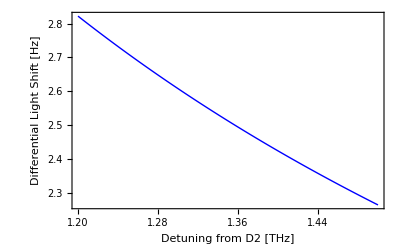
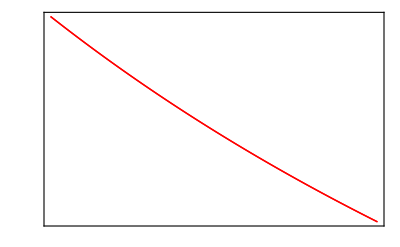

```mathematica
DIFF = Plot[DLSinHz[Δ*10^12,4,5,PerturbationIntensity[.1,5]]/.q ->-1,{Δ,1.2,1.5},PlotStyle->Blue ,Axes->False,FrameLabel->{"Detuning from D2 [THz]", "Differential Light Shift [Hz]"},ImagePadding->50,Frame->{True,True,True,False},FrameStyle->{Automatic,Blue,Automatic,Automatic}];
ABS =Plot[{HFLightshift[Δ*10^12,4,PerturbationIntensity[.1,5]],HFLightshift[Δ*10^12,5,PerturbationIntensity[.1,5]]}/.q ->-1,{Δ,1.2,1.5},PlotStyle->Red ,ImagePadding->50,Axes->True,Frame->{False,False,False,True},FrameTicks->{None,None,None,All},FrameStyle->{Automatic,Automatic,Automatic,Red}];
Overlay[{DIFF,ABS}]
```

```mathematica
HEAT =LogPlot[HFHeating[Δ*10^12,4,PerturbationIntensity[.1,5]]/.q->-1,{Δ,1.2,1.5},PlotStyle->{Magenta,Thick} ,ImagePadding->50,Axes->False,Frame->{False,False,False,True},FrameTicks->{None,None,None,All},FrameStyle->{Automatic,Automatic,Automatic,Magenta}];
```

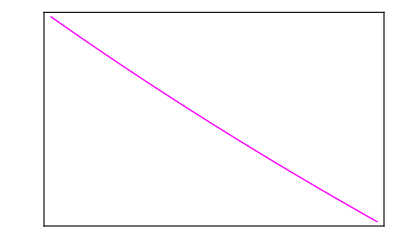
-Graphics--Graphics-

```mathematica
Overlay[{DIFF,HEAT}]
```

```mathematica
TwoAxisPlot[{f_,g_},{x_,x1_,x2_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[Plot[#,{x,x1,x2},Axes->True,PlotStyle->{ColorData[1][#2[[1]]],Thick}]&,{f,g}];{frange,grange}=(PlotRange/.AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};fticks=N@FindDivisions[frange,5];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]]
```

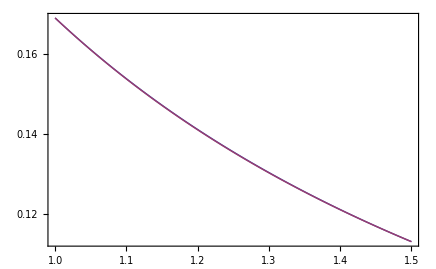

```mathematica
TwoAxisPlot[{DLSinHz[Δ*10^12,4,5,PerturbationIntensity[.005,5]]/.q ->-1,HFLightshift[Δ*10^12,4,PerturbationIntensity[.005,5]]/.q ->-1},{Δ,1,1.5}]
```

## Light Shifts for small detuning (resolved hyperfine states)

```mathematica
ACStark[Δ_,m_,I_] := -1/(2 hbar hPlanck  ϵ c)( μD1^2/2 I Sum[(1/(Subscript[ν, D1]-energies⟦m⟧MHz+energiesD1⟦j⟧MHz-(Subscript[ν, D1]  +Δ))+1/(2 Subscript[ν, D1]-energies⟦m⟧MHz+energiesD1⟦j⟧MHz+Δ))D1TransitionElements⟦m,j⟧^2,{j,18}]+μD2^2/4 I Sum[(1/(Subscript[ν, D2]-energies⟦m⟧MHz+energiesD2⟦j⟧MHz-(Subscript[ν, D1]  +Δ))+1/(Subscript[ν, D2]-energies⟦m⟧MHz+energiesD2⟦j⟧MHz+(Subscript[ν, D1]  +Δ)))D2TransitionElements⟦m,j⟧^2,{j,36}])
```

Part::partw: Part 7 of {-475.395, -466.705, -457.849, 458.012, 466.702, 475.235} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partw: Part 7 of {-475.395, -466.705, -457.849, 458.012, 466.702, 475.235} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partw: Part 7 of {-475.395, -466.705, -457.849, 458.012, 466.702, 475.235} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

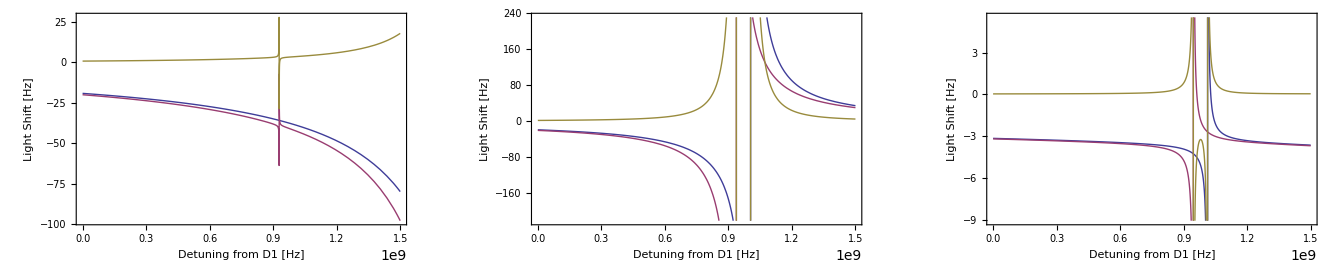

```mathematica
D1σPlus = Plot[{(ACStark[Δ,1,1 ]/.q ->1),( ACStark[Δ,2,1 ]/.q ->1),(ACStark[Δ,1,1 ]/.q ->1)-(ACStark[Δ,2,1 ]/.q ->1)},{Δ,-0GHz,1.5GHz},PlotStyle->Thick ,Frame -> True,FrameLabel->{"Detuning from D1 [Hz]", "Light Shift [Hz]"}];
D1π = Plot[{(ACStark[Δ,1,1 ]/.q ->0),( ACStark[Δ,2,1 ]/.q ->0),(ACStark[Δ,1,1 ]/.q ->0)-(ACStark[Δ,2,1 ]/.q ->0)},{Δ,-0GHz,1.5GHz},PlotStyle->Thick ,Frame -> True,FrameLabel->{"Detuning from D1 [Hz]", "Light Shift [Hz]"}];
D1σMinus = Plot[{(ACStark[Δ,1,1 ]/.q ->-1),( ACStark[Δ,2,1 ]/.q ->-1),(ACStark[Δ,1,1 ]/.q ->-1)-(ACStark[Δ,2,1 ]/.q ->-1)},{Δ,-0GHz,1.5GHz},PlotStyle->Thick ,Frame -> True,FrameLabel->{"Detuning from D1 [Hz]", "Light Shift [Hz]"}];
GraphicsRow[{D1σPlus,D1π,D1σMinus }]
```

Part::partw: Part 7 of {-475.395, -466.705, -457.849, 458.012, 466.702, 475.235} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partw: Part 7 of {-475.395, -466.705, -457.849, 458.012, 466.702, 475.235} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partw: Part 7 of {-475.395, -466.705, -457.849, 458.012, 466.702, 475.235} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

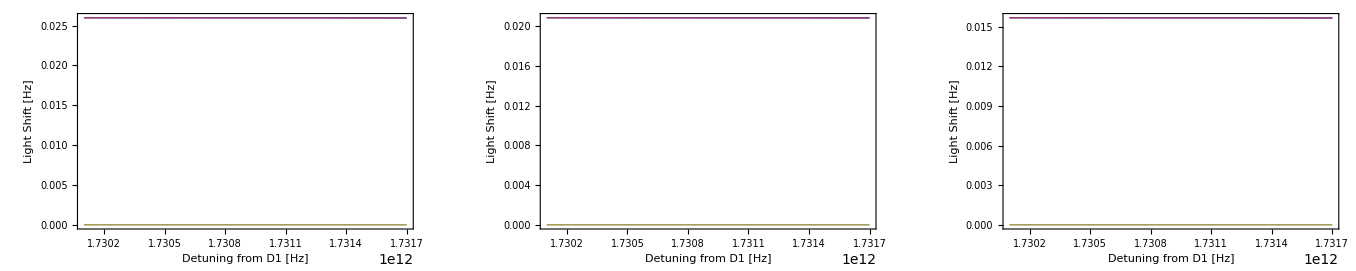

```mathematica
D2σPlus = Plot[{(ACStark[Δ,1,1 ]/.q ->1),( ACStark[Δ,2,1 ]/.q ->1),(ACStark[Δ,1,1 ]/.q ->1)-(ACStark[Δ,2,1 ]/.q ->1)},{Δ,1730.1GHz, 1731.7GHz},PlotStyle->Thick ,Frame -> True,FrameLabel->{"Detuning from D1 [Hz]", "Light Shift [Hz]"}];
D2π = Plot[{(ACStark[Δ,1,1 ]/.q ->0),( ACStark[Δ,2,1 ]/.q ->0),(ACStark[Δ,1,1 ]/.q ->0)-(ACStark[Δ,2,1 ]/.q ->0)},{Δ,1730.1GHz, 1731.7GHz},PlotStyle->Thick ,Frame -> True,FrameLabel->{"Detuning from D1 [Hz]", "Light Shift [Hz]"}];
D2σMinus = Plot[{(ACStark[Δ,1,1 ]/.q ->-1),( ACStark[Δ,2,1 ]/.q ->-1),(ACStark[Δ,1,1 ]/.q ->-1)-(ACStark[Δ,2,1 ]/.q ->-1)},{Δ,1730.1GHz, 1731.7GHz},PlotStyle->Thick ,Frame -> True,FrameLabel->{"Detuning from D1 [Hz]", "Light Shift [Hz]"}];
GraphicsRow[{D2σPlus,D2π,D2σMinus }]
```

```mathematica
ACHeating[Δ_,m_,I_]:=(2((Subscript[ν, D1]+Δ))^3)/(hbar^3 c^3 π 3 ϵ^1)(μD1^4/2 I Sum[(1/(-Δ-energies⟦m⟧MHz+energiesD1⟦j⟧MHz)+1/(2 Subscript[ν, D1]-energies⟦m⟧MHz+energiesD1⟦j⟧MHz+Δ))^2 D1TransitionElements⟦m,j⟧^2/(1(*+4((Subscript[ν, D1]  +Δ)-energies⟦m⟧MHz+energiesD1⟦j⟧MHz)^2/Γ[K40,1]^2*)),{j,18}]+μD2^4/4 I Sum[(1/(Subscript[ν, D2]-energies⟦m⟧MHz+energiesD2⟦j⟧MHz-(Subscript[ν, D1]  +Δ))+1/(Subscript[ν, D2]-energies⟦m⟧MHz+energiesD2⟦j⟧MHz+(Subscript[ν, D1]  +Δ)))^2 D2TransitionElements⟦m,j⟧^2/(1(*+4((Subscript[ν, D1]  +Δ)-energies⟦m⟧MHz+energiesD2⟦j⟧MHz)^2/Γ[K40,2]^2*)),{j,36}])
```

```mathematica
LogPlot[{( ACHeating[Δ GHz,3,1 ]/.q ->0)},{Δ,-1,2},PlotRange ->All,PlotStyle->Thick ,Frame -> True,FrameLabel->{"Detuning from D1 [GHz]", "Heating Rate[1/s]"}];
```

Part::partw: Part 7 of {-475.395, -466.705, -457.849, 458.012, 466.702, 475.235} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
q = 0;
Summe =(ACHeating[Δ,1,1 ]+ ACHeating[Δ,2,1 ]+ACHeating[Δ,3,1 ]);
D2Lines =LogPlot[{( ACHeating[Δ,1,1]),( ACHeating[Δ,2,1]),(ACHeating[Δ,3,1]),HFHeating[Δ,1,1]},{Δ,1730.1GHz, 1731.5GHz},PlotRange -> All,PlotStyle->{{Thick,Dotted},{Thick,Dotted},{Thick,Dotted},Black},Frame -> True,FrameLabel->{"Detuning from D1 [Hz]", "Heating Rate[1/s]"}];
D2SummedSpectrum = LogPlot[Summe,{Δ,1730.1GHz, 1731.5GHz},PlotRange -> All,PlotStyle->{Thick,Green} ,Frame -> True,FrameLabel->{"Detuning from D1 [Hz]", "Heating Rate[1/s]"}];
D1Lines =LogPlot[{( (1-Abs[q])ACHeating[Δ,1,1]),( ACHeating[Δ,2,1]),(ACHeating[Δ,3,1]),HFHeating[Δ,2,1]},{Δ,-1.5GHz,1GHz},PlotRange -> All,PlotStyle->{{Thick,Dotted},{Thick,Dotted},{Thick,Dotted},Black},Frame -> True,FrameLabel->{"Detuning from D1 [Hz]", "Heating Rate[1/s]"}];
D1SummedSpectrum = LogPlot[Summe,{Δ,-1.5GHz, 1GHz},PlotRange -> All,PlotStyle->{Thick,Green} ,Frame -> True,FrameLabel->{"Detuning from D1 [Hz]", "Heating Rate[1/s]"}];
Clear[q]
```

Part::partw: Part 7 of {-475.395, -466.705, -457.849, 458.012, 466.702, 475.235} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partw: Part 7 of {-475.395, -466.705, -457.849, 458.012, 466.702, 475.235} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partw: Part 7 of {-475.395, -466.705, -457.849, 458.012, 466.702, 475.235} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

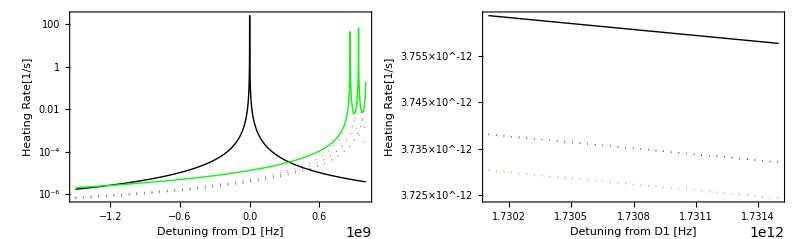

```mathematica
GraphicsRow[{Show[D1Lines, D1SummedSpectrum],Show[D2Lines, D2SummedSpectrum]}]
```

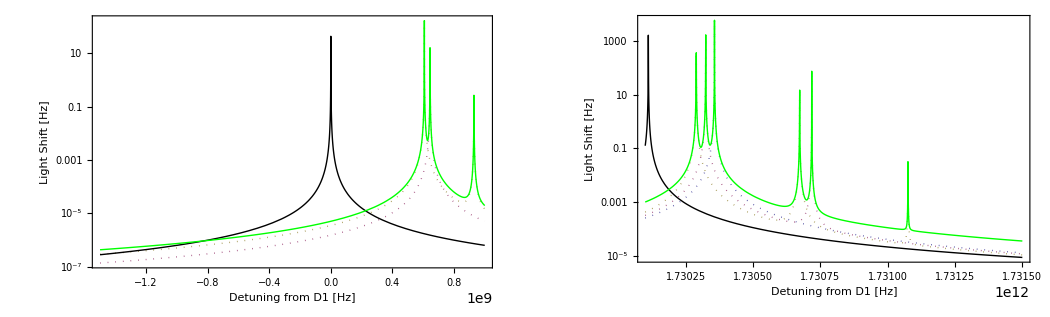

-Graphics-

```mathematica
(*Clear[m]
D2Spec = LogPlot[Sum[ACHeating[Δ,m,1 ]/.q-> -1,{m,1,18}],{Δ,1727GHz, 1731.5GHz},PlotRange -> All,PlotStyle->Thick ,Frame -> True,FrameLabel->{"Detuning from D1 [Hz]", "Light Shift [Hz]"}];
D1Spec = LogPlot[{Sum[ACHeating[Δ,m,1 ]/.q-> -1,{m,1,18}]},{Δ,-2GHz, 2GHz},PlotRange -> All,PlotStyle->Thick ,Frame -> True,FrameLabel->{"Detuning from D1 [Hz]", "Light Shift [Hz]"}];
GraphicsRow[{D1Spec,D2Spec}]*)
```